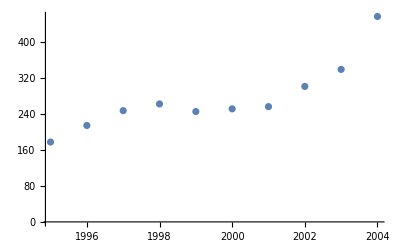

{x_0→-1.27736×10^10,x_1→1.91714×10^7,x_2→-9591.22,x_3→1.59946}

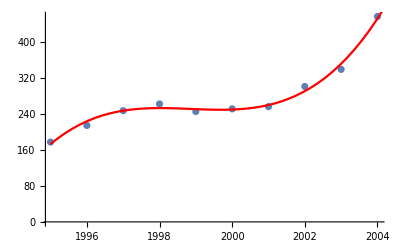

```mathematica
(* Задача 1 б) *)
data={
{1995,178},
{1996,215},
{1997,248},
{1998,263},
{1999,246},
{2000,252},
{2001,257},
{2002,302},
{2003,340},
{2004,458}};
dataPlot=ListPlot[data]
(* A third degree polynomial might be close to the real curve, so we will use least squares with it *)
polyDeg=3;
BasisForPolynomials[n_?NumberQ]:=Table[With[{i=k},#^i&],{k,0,n}]
polyBasis=BasisForPolynomials[polyDeg];
q=Table[Subscript[x, i],{i,0,polyDeg}];
(*Minimize[Sum[(Subscript[q, i] polyBasis@data⟦i⟧⟦1⟧ - data⟦i⟧⟦2⟧),{i,1,Length@data}],q]*)
{mininimum,minCoeffs}=Minimize[Sum[(q . ((#@data⟦i⟧⟦1⟧)&/@polyBasis )- data⟦i⟧⟦2⟧)^2,{i,1,Length@data}],q];
N@minCoeffs
polynomialPlot=Plot[(q/.minCoeffs).((#@x)&/@polyBasis),{x,data⟦1⟧⟦1⟧,data⟦-1⟧⟦1⟧+1},PlotStyle->Red];
Show[{dataPlot,polynomialPlot}]
```

```mathematica
ExampleData[{"TestImage","Lena"}];
```

-Graphics-